## SGN, VN

```mathematica
SGNCasesDataRaw={1,2,3,0,0,0,1,1,0,36,25,29,59,0,70,31,30,26,31,31,46,39,40,61,48,84,95,82,90,99,137,149,135,137,166,136,152,162,724,58,200,218,155,249,464,419,714,599,641,710,766,915,1229,1320,1397};
```

```mathematica
SGNCasesDataRaw//Accumulate
```

{1,3,6,6,6,6,7,8,8,44,69,98,157,157,227,258,288,314,345,376,422,461,501,562,610,694,789,871,961,1060,1197,1346,1481,1618,1784,1920,2072,2234,2958,3016,3216,3434,3589,3838,4302,4721,5435,6034,6675,7385,8151,9066,10295,11615,13012}

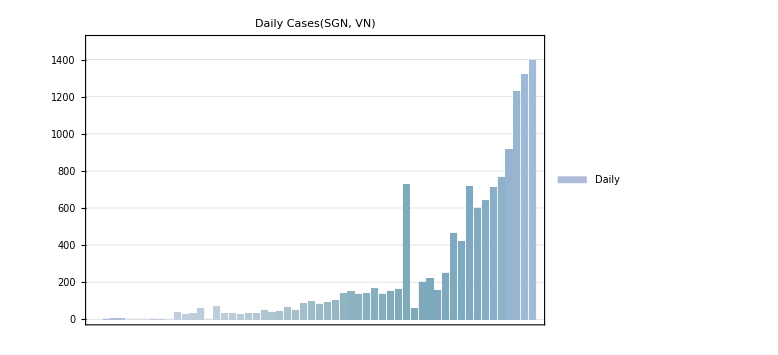

```mathematica
BarChart[SGNCasesDataRaw,PlotTheme->{"Detailed","FrameGrid"},ChartLegends->{"Daily"},PlotLabel->HoldForm["Daily Cases(SGN, VN)"],LabelStyle->{FontFamily->"Consolas",13,GrayLevel[0],Bold},PlotRange->{0,1500},ImageSize->Large,ChartStyle->"Aquamarine"]
```

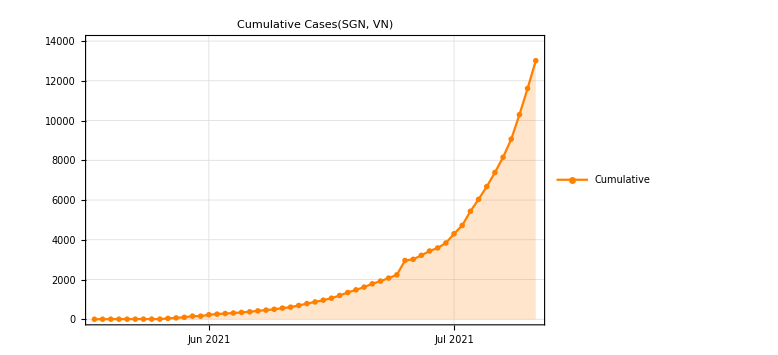

```mathematica
rifflingValues[entities_,values_]:=Partition[Flatten[Map[Function[Most[#]],MapThread[Riffle,{Map[Function[Append[#,-1]],entities],values}]]],2]
SGNDateDateRaw=Partition[DateRange[DateObject[{2021,5,18}],DateObject[{2021,7,11}]],1];
DateListPlot[rifflingValues[SGNDateDateRaw,SGNCasesDataRaw//Accumulate],PlotTheme->{"Monochrome","FrameGrid"},PlotLegends->{"Cumulative"},PlotStyle->Orange,Filling->Axis,PlotLabel->HoldForm["Cumulative Cases(SGN, VN)"],LabelStyle->{FontFamily->"Consolas",13,GrayLevel[0],Bold},PlotRange->{0,14000},ImageSize->Large]
```

```mathematica
RichardsGrowthCurve[θ1_,θ2_,θ3_,ξ_,x_]:=θ1/((1+ξ*E^(-θ2*(x-θ3)))^(1/ξ))
```

```mathematica
accpts=rifflingValues[Partition[Range[SGNCasesDataRaw//Length],1],SGNCasesDataRaw//Accumulate]
```

{{1,1},{2,3},{3,6},{4,6},{5,6},{6,6},{7,7},{8,8},{9,8},{10,44},{11,69},{12,98},{13,157},{14,157},{15,227},{16,258},{17,288},{18,314},{19,345},{20,376},{21,422},{22,461},{23,501},{24,562},{25,610},{26,694},{27,789},{28,871},{29,961},{30,1060},{31,1197},{32,1346},{33,1481},{34,1618},{35,1784},{36,1920},{37,2072},{38,2234},{39,2958},{40,3016},{41,3216},{42,3434},{43,3589},{44,3838},{45,4302},{46,4721},{47,5435},{48,6034},{49,6675},{50,7385},{51,8151},{52,9066},{53,10295},{54,11615},{55,13012}}

```mathematica
BezierLine=BezierFunction[accpts]
```

BezierFunction[…]

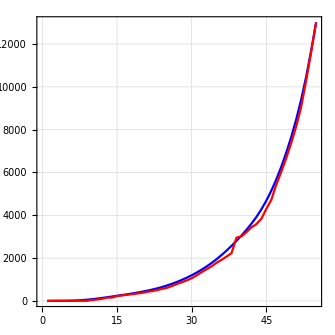

```mathematica
BezierPts=Round[Last[#]&/@Map[Function[BezierLine[#]],Range[1/(accpts//Length),1,1/(accpts//Length)]]];
ListLinePlot[{BezierPts,SGNCasesDataRaw//Accumulate},PlotStyle->{Blue,Red},PlotTheme->{"Scientific","FrameGrid"},AspectRatio->1]
```

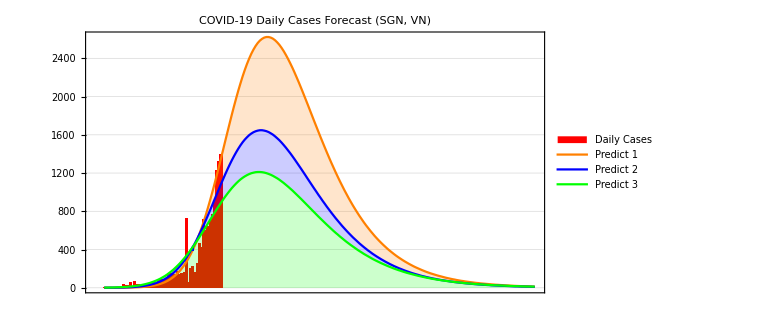

```mathematica
Show [BarChart[Join[SGNCasesDataRaw,Table[0,200-Length[SGNCasesDataRaw]]],ChartLegends->{"Daily Cases"},ChartStyle->Red,PlotTheme->{"Business","FrameGrid"}],
ListLinePlot[{
Round[Table[RichardsGrowthCurve[150000,0.052,77,0.19,x+1]-RichardsGrowthCurve[150000,0.052,77,0.19,x],{x,1,200}]],
Round[Table[RichardsGrowthCurve[100000,0.049,74,0.19,x+1]-RichardsGrowthCurve[100000,0.049,74,0.19,x],{x,1,200}]],
Round[Table[RichardsGrowthCurve[80000,0.045,73,0.19,x+1]-RichardsGrowthCurve[80000,0.045,73,0.19,x],{x,1,200}]]
},Filling->{1->{2},2->{3},3->Axis},PlotLegends->{"Predict 1","Predict 2","Predict 3"},PlotStyle->{Orange,Blue,Green}],PlotLabel->HoldForm["COVID-19 Daily Cases Forecast (SGN, VN)"],LabelStyle->{FontFamily->"Consolas",13,GrayLevel[0],Bold},ImageSize->Large,AspectRatio->1/1.8]
```

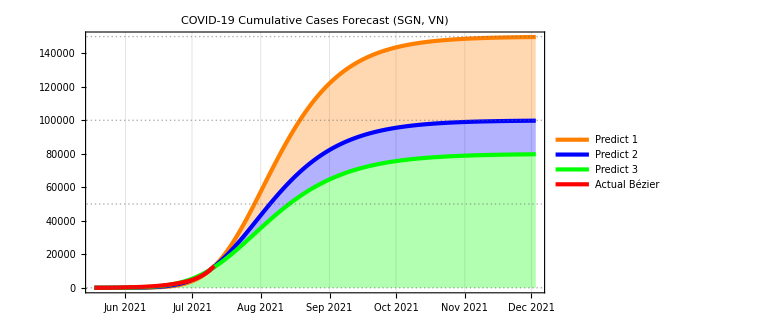

```mathematica
DateListPlot[{
rifflingValues[Partition[DateRange[DateObject[{2021,5,18}],DateObject[{2021,12,3}]],1],Round[Table[RichardsGrowthCurve[150000,0.052,77,0.19,x],{x,1,200}]]],
rifflingValues[Partition[DateRange[DateObject[{2021,5,18}],DateObject[{2021,12,3}]],1],Round[Table[RichardsGrowthCurve[100000,0.049,74,0.19,x],{x,1,200}]]],rifflingValues[Partition[DateRange[DateObject[{2021,5,18}],DateObject[{2021,12,3}]],1],Round[Table[RichardsGrowthCurve[80000,0.045,73,0.19,x],{x,1,200}]]],rifflingValues[Partition[DateRange[DateObject[{2021,5,18}],DateObject[{2021,7,11}]],1],BezierPts]
},
PlotTheme->{"Business","FrameGrid"},PlotLegends->{"Predict 1","Predict 2","Predict 3","Actual Bézier"},PlotStyle->{Orange,Blue,Green,Red},Filling->{1->{2},2->{3},3->Axis},ImageSize->Large,AspectRatio->1/1.8,PlotLabel->HoldForm["COVID-19 Cumulative Cases Forecast (SGN, VN)"],LabelStyle->{FontFamily->"Consolas",13,GrayLevel[0],Bold}]
```

## Vietnam

```mathematica
AllData={6,7,7,8,10,0,18,64,41,80,92,125,70,82,72,104,166,187,181,152,175,114,131,143,129,184,444,235,227,253,277,250,211,250,229,231,219,246,201,211,171,381,211,185,259,293,266,398,414,503,259,471,300,267,229,217,279,845,164,314,382,361,441,693,527,914,873,1089,1019,997,1307,1616,1844,1945};
```

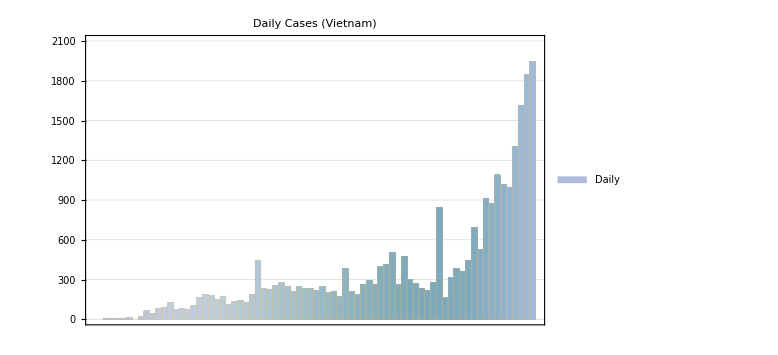

```mathematica
BarChart[AllData,PlotTheme->{"Detailed","FrameGrid"},ChartLegends->{"Daily"},PlotLabel->HoldForm["Daily Cases (Vietnam)"],LabelStyle->{FontFamily->"Consolas",13,GrayLevel[0],Bold},PlotRange->{0,2100},ImageSize->Large,ChartStyle->"Aquamarine"]
```

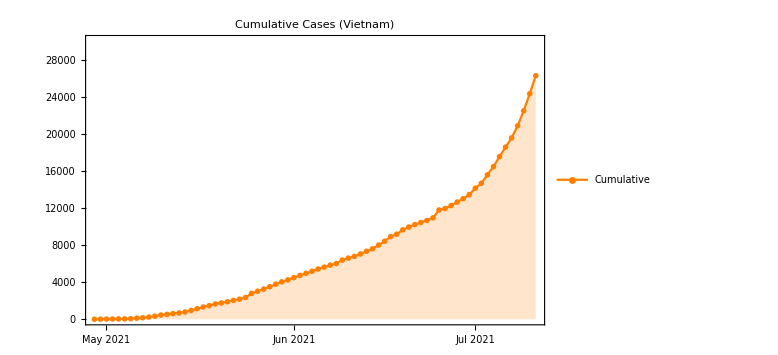

```mathematica
DateListPlot[rifflingValues[Partition[DateRange[DateObject[{2021,4,29}],DateObject[{2021,7,11}]],1],AllData//Accumulate],PlotTheme->"Monochrome",PlotLegends->{"Cumulative"},PlotStyle->Orange,Filling->Axis,PlotLabel->HoldForm["Cumulative Cases (Vietnam)"],LabelStyle->{FontFamily->"Consolas",13,GrayLevel[0],Bold},PlotRange->{0,30000},ImageSize->Large]
```

```mathematica
TheRestData=PadLeft[Take[AllData -PadLeft[SGNCasesDataRaw,74],Length[AllData]-Length[SGNCasesDataRaw]],29];
```

```mathematica
bezierfunc=BezierFunction[rifflingValues[Partition[Range[1,TheRestData//Length],1],TheRestData//Accumulate]];
bezierpts=Last[#]&/@Map[Function[bezierfunc[#]],Range[1/(TheRestData//Length),1,1/(TheRestData//Length)]]//Round;
```

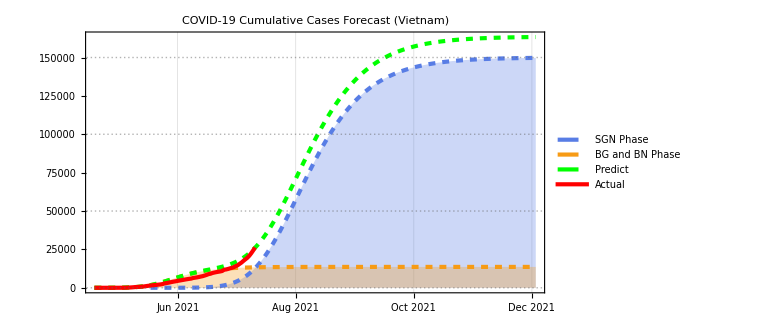

```mathematica
DateListPlot[{
rifflingValues[Partition[DateRange[DateObject[{2021,5,18}],DateObject[{2021,12,3}]],1],Round[Table[RichardsGrowthCurve[150000,0.052,77,0.19,x],{x,1,200}]]],
rifflingValues[Partition[DateRange[DateObject[{2021,4,19}],DateObject[{2021,12,3}]],1],Round[Table[RichardsGrowthCurve[13600,0.09,41,0.25,x],{x,1,229}]]],
rifflingValues[Partition[DateRange[DateObject[{2021,4,19}],DateObject[{2021,12,3}]],1],Join[Take[Round[Table[RichardsGrowthCurve[13600,0.09,41,0.25,x],{x,1,229}]],29],Drop[Round[Table[RichardsGrowthCurve[13600,0.09,41,0.25,x],{x,1,229}]],29]+Round[Table[RichardsGrowthCurve[150000,0.052,77,0.19,x],{x,1,200}]]]],
rifflingValues[Partition[DateRange[DateObject[{2021,4,19}],DateObject[{2021,7,11}]],1],Accumulate[PadLeft[AllData,84]]]
},PlotTheme->{"Business","FrameGrid"},PlotLegends->{"SGN Phase","BG and BN Phase","Predict","Actual"},PlotStyle->{{Dashed},{Dashed},{Dashed,Green},{Red}},Filling->{1->Axis,2->Axis},ImageSize->Large,AspectRatio->1/1.8,PlotLabel->HoldForm["COVID-19 Cumulative Cases Forecast (Vietnam)"],LabelStyle->{FontFamily->"Consolas",13,GrayLevel[0],Bold}]
```

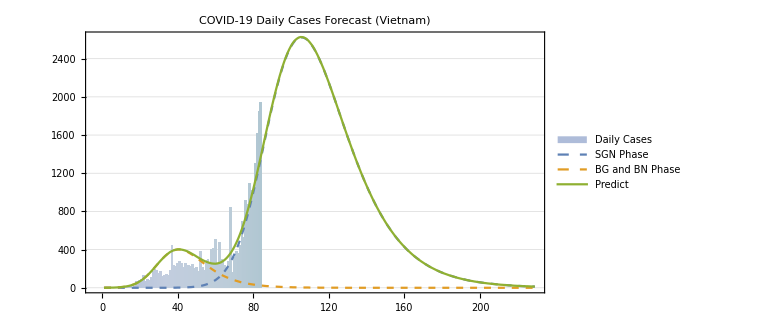

```mathematica
Show [BarChart[Join[Table[0,10],AllData,Table[0,219-Length[AllData]]],ChartLegends->{"Daily Cases"},ChartStyle->"Aquamarine",PlotTheme->{"Business","FrameGrid"}],
ListLinePlot[{
Join[Table[0,29],Round[Table[RichardsGrowthCurve[150000,0.052,77,0.19,x+1]-RichardsGrowthCurve[150000,0.052,77,0.19,x],{x,1,200}]]],
Round[Table[RichardsGrowthCurve[13600,0.09,41,0.25,x+1]-RichardsGrowthCurve[13600,0.09,41,0.25,x],{x,1,229}]],
Join[Take[Round[Table[RichardsGrowthCurve[13600,0.09,41,0.25,x+1]-RichardsGrowthCurve[13600,0.09,41,0.25,x],{x,1,229}]],29],Drop[Round[Table[RichardsGrowthCurve[13600,0.09,41,0.25,x+1]-RichardsGrowthCurve[13600,0.09,41,0.25,x],{x,1,229}]],29]+Round[Table[RichardsGrowthCurve[150000,0.052,77,0.19,x+1]-RichardsGrowthCurve[150000,0.052,77,0.19,x],{x,1,200}]]]
},PlotLegends->{"SGN Phase","BG and BN Phase","Predict"},PlotStyle->{{Dashed},{Dashed},{Thick}}],ImageSize->Large,AspectRatio->1/1.8,PlotLabel->HoldForm["COVID-19 Daily Cases Forecast (Vietnam)"],LabelStyle->{FontFamily->"Consolas",13,GrayLevel[0],Bold}]
```